```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/silvestre_parameters.nb"];
NotebookEvaluate["modules/find_minimum.nb"];
On[Assert]
```

```mathematica
data={};
For[g=1,g≤2,g++,
Print[g];
ClearAll[J,P,Isospin,γMax,Λ,m1,m2,m3,projector,project,size,firstNonZero];
(* INITIALISE HYPERPARAMETERS AND OBTAIN LOWEST LYING STATE *)
(**** !!!TUNABLE PARAMETERS!!! ****)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=0;(* Isospin *)
γMax=g*2;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
m1=uq;(* mass of quark 1 *)
m2=sq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)

(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
If[m1==m2,project=True,project=False];

(* Obtain projector matrix *)
projector=Projector[J,P,Λ,γMax,Isospin];

(* Calculate generalised transformation matrices *)
{t1time,t1}=Timing[tMatrix[J,P,Λ,γMax,m1,m2,m3,1]];
Print["Time taken to compute t1: ",t1time];
{t2time,t2}=Timing[tMatrix[J,P,Λ,γMax,m1,m2,m3,2]];
Print["Time taken to compute t2: ",t2time];

(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];

(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
If[project==True,firstNonZero=size-Total[Diagonal[projector]]+1,firstNonZero=1];
min=findMinimum[];
AppendTo[data,{size,min[[2]]}]
]
```

1

Time taken to compute t1: 0.057218

Time taken to compute t2: 0.046768

ΔE smaller than 1x10^-6, breaking search after 6 steps. ΔE: 1.16994×10^-8

{ω_min, E_min}: {0.455733,2.49353}

2

Time taken to compute t1: 0.235624

Time taken to compute t2: 0.218339

ΔE smaller than 1x10^-6, breaking search after 6 steps. ΔE: 3.10243×10^-8

{ω_min, E_min}: {0.526994,2.47244}

```mathematica
data
```

{{8,2.49353},{20,2.47244}}

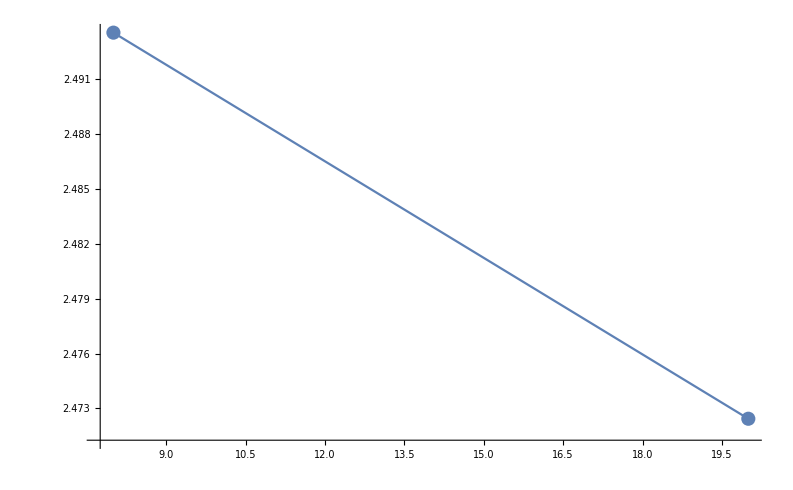

```mathematica
ListPlot[data,Joined->True,PlotMarkers->All,PlotRange->All]
```